```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["Infrastructure.m"];
Get["MMA2TxtFormat3.m"];
```

# Data generation

## Generating single variable polynomial dataset ( split & non split )

### Sample single variable polynomials for split and non split data

```mathematica
(* Generating polynomial data *)
(* Original polynomial has max degree 2 and max coefficient size 5 *)
(* Substitution polynomial has max degree 4 and max coefficient size 20 *)
Generate$data1and2$CommonSet[n_]:=
Monitor[
Table[RandomPolynomialWithSplit2$PolyNInPoly2$LSS[5,2,20,4,{a[1]}],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
Generate$data1and2$CommonSet[10]//TableForm
```

-1389+2086 a[1]-39 a[1]^2-1603 a[1]^3+833 a[1]^4+168 a[1]^5-236 a[1]^6+56 a[1]^7-4 a[1]^8 | -1225+-164+2086 a[1]+-39 a[1]^2+-248 a[1]^3+-1355 a[1]^3+250 a[1]^4+583 a[1]^4+134 a[1]^5+34 a[1]^5+-236 a[1]^6+56 a[1]^7+-a[1]^8+-3 a[1]^8 | -2-3 s-4 s^2 | -19+14 a[1]+5 a[1]^2-7 a[1]^3+a[1]^4
-22-88 a[1]+35 a[1]^2+133 a[1]^3-97 a[1]^4+18 a[1]^5-a[1]^6 | -7+-15+-23 a[1]+-65 a[1]+35 a[1]^2+133 a[1]^3+-91 a[1]^4+-6 a[1]^4+18 a[1]^5+-a[1]^6+0 | 2-5 s-s^2 | 3+8 a[1]-9 a[1]^2+a[1]^3
-450+765 a[1]-239 a[1]^2-72 a[1]^3-4 a[1]^4 | -450+765 a[1]+-32 a[1]^2+-207 a[1]^2+-65 a[1]^3+-7 a[1]^3+-4 a[1]^4 | 1-3 s-4 s^2 | -11+9 a[1]+a[1]^2
-1802-950 a[1]-1265 a[1]^2-1820 a[1]^3-390 a[1]^4-430 a[1]^5-260 a[1]^6+80 a[1]^7-5 a[1]^8 | -1068+-734+-950 a[1]+-484 a[1]^2+-781 a[1]^2+-1820 a[1]^3+-390 a[1]^4+-157 a[1]^5+-273 a[1]^5+-221 a[1]^6+-39 a[1]^6+80 a[1]^7+-5 a[1]^8 | 3-5 s^2 | -19-5 a[1]-6 a[1]^2-8 a[1]^3+a[1]^4
705+1350 a[1]+1323 a[1]^2+723 a[1]^3+234 a[1]^4+36 a[1]^5+2 a[1]^6 | 80+625+1350 a[1]+121 a[1]^2+1202 a[1]^2+723 a[1]^3+53 a[1]^4+181 a[1]^4+36 a[1]^5+2 a[1]^6 | 2-s+2 s^2 | 19+18 a[1]+9 a[1]^2+a[1]^3
370+770 a[1]-678 a[1]^2-1813 a[1]^3-13 a[1]^4+928 a[1]^5+436 a[1]^6+72 a[1]^7+4 a[1]^8 | 370+770 a[1]+-383 a[1]^2+-295 a[1]^2+-1609 a[1]^3+-204 a[1]^3+-6 a[1]^4+-7 a[1]^4+284 a[1]^5+644 a[1]^5+29 a[1]^6+407 a[1]^6+66 a[1]^7+6 a[1]^7+4 a[1]^8 | 1-5 s+4 s^2 | -9-10 a[1]+14 a[1]^2+9 a[1]^3+a[1]^4
60-60 a[1]+31 a[1]^2-8 a[1]^3+a[1]^4 | 60+-60 a[1]+31 a[1]^2+-6 a[1]^3+-2 a[1]^3+a[1]^4 | 4+s+s^2 | 7-4 a[1]+a[1]^2
-917+726 a[1]-628 a[1]^2+313 a[1]^3-112 a[1]^4+32 a[1]^5-4 a[1]^6 | -917+319 a[1]+407 a[1]+-628 a[1]^2+313 a[1]^3+-112 a[1]^4+32 a[1]^5+-3 a[1]^6+-a[1]^6 | -2+s-4 s^2 | -15+6 a[1]-4 a[1]^2+a[1]^3
-50-210 a[1]-221 a[1]^2-40 a[1]^3-2 a[1]^4 | -30+-20+-210 a[1]+-221 a[1]^2+-40 a[1]^3+-a[1]^4+-a[1]^4 | 5-s-2 s^2 | 5+10 a[1]+a[1]^2
410-912 a[1]-115 a[1]^2+761 a[1]^3+178 a[1]^4-44 a[1]^5+2 a[1]^6 | 410+-66 a[1]+-846 a[1]+-115 a[1]^2+761 a[1]^3+178 a[1]^4+-9 a[1]^5+-35 a[1]^5+2 a[1]^6 | 4+s+2 s^2 | 14-16 a[1]-11 a[1]^2+a[1]^3

```mathematica
data1and2$CommonSet=Generate$data1and2$CommonSet[130000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
data1and2$CommonSet=DeleteDuplicatesBy[data1and2$CommonSet,First];
Length[data1and2$CommonSet]
```

128902

### Tokenize non split data from the sampled polynomials

```mathematica
Get["MMA2TxtFormat3.m"];
Generate$data1$format3[n_]:=
Monitor[
Table[
{long,longsplit,short,sub}=data1and2$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
data1$format3=Generate$data1$format3[120000];
```

```mathematica
data1$format3⟦1;;3⟧
```

{+ P 2 1 + * P 1 2 0 a1 + * P 1 2 4 ^ a1 P 2 + * N 4 8 ^ a1 P 3 * P 4 ^ a1 P 4 ? + N 2 + * N 6 a1 ^ a1 P 2,+ N 2 0 7 7 + * N 3 8 7 6 a1 + * N 1 6 0 1 ^ a1 P 2 + * P 1 9 0 ^ a1 P 3 * N 5 ^ a1 P 4 ? + N 2 0 + * N 1 9 a1 ^ a1 P 2,+ P 3 8 5 + * P 7 8 a1 + * N 5 8 1 ^ a1 P 2 + * P 6 8 1 ^ a1 P 3 + * P 3 4 0 ^ a1 P 4 + * N 5 6 6 ^ a1 P 5 + * P 3 3 1 ^ a1 P 6 + * P 3 8 ^ a1 P 7 ^ a1 P 8 ? + P 1 9 + * P 2 a1 + * N 1 5 ^ a1 P 2 + * P 1 9 ^ a1 P 3 ^ a1 P 4}

```mathematica
(* token data information *)
```

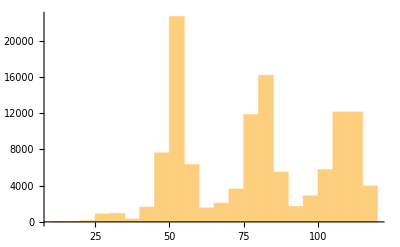

119

32

```mathematica
StringSplit/@data1$format3;
Length/@%//Histogram
Length/@%%//Max
Map[Function[sublist,Part[sublist,Position[sublist,"?"][[1,1]]+1;;]],%%%];
Length/@%//Max
```

### Tokenize split data from the sampled polynomials

```mathematica
Get["MMA2TxtFormat3.m"];
Generate$data2$format3[n_]:=Monitor[Flatten[Table[
{longExpand,longSplit,short,sub}=data1and2$CommonSet⟦i⟧;
expandedForm=MMAExprToJFString[longExpand]<>" ? "<>MMAExprToJFString[sub];
splitForm=MMAExprToJFStringNonExpand[longSplit]<>" ? "<>MMAExprToJFString[sub];
{expandedForm,splitForm},{i,n}],1],Row[{"Generating element: ",i}]]
```

```mathematica
data2$format3=Generate$data2$format3[50000];
Length[data2$format3]
```

100000

```mathematica
data2$format3⟦1;;2⟧
```

{+ P 2 1 + * P 1 2 0 a1 + * P 1 2 4 ^ a1 P 2 + * N 4 8 ^ a1 P 3 * P 4 ^ a1 P 4 ? + N 2 + * N 6 a1 ^ a1 P 2,+ P 1 7 + P 4 + * P 1 2 0 a1 + * P 1 2 4 ^ a1 P 2 + * N 1 1 ^ a1 P 3 + * N 3 7 ^ a1 P 3 + * P 3 ^ a1 P 4 ^ a1 P 4 ? + N 2 + * N 6 a1 ^ a1 P 2}

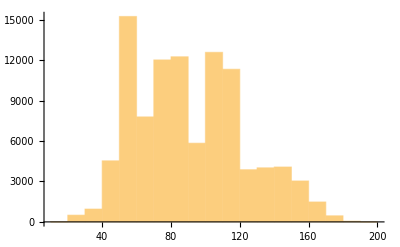

195

32

```mathematica
StringSplit/@data2$format3;
Length/@%//Histogram
Length/@%%//Max
Map[Function[sublist,Part[sublist,Position[sublist,"?"][[1,1]]+1;;]],%%%];
Length/@%//Max
```

### Save dataset

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/repos/PolynomialSubstructure/MMA_package

```mathematica
Export["data_storage/dataset/example_single/single_variable_test.txt",data1$format3⟦1;;3000⟧,"Text"]
Export["data_storage/dataset/example_single/single_variable_valid.txt",data1$format3⟦3001;;3128⟧,"Text"]
Export["data_storage/dataset/example_single/nonsplit_data_train.txt",data1$format3⟦3129;;103128⟧,"Text"]
Export["data_storage/dataset/example_single/split_data_train.txt",data2$format3⟦1;;100000⟧,"Text"]
```

data_storage/dataset/example_single/single_variable_test.txt

data_storage/dataset/example_single/single_variable_valid.txt

data_storage/dataset/example_single/nonsplit_data_train.txt

data_storage/dataset/example_single/split_data_train.txt

## Generating O(N) dataset

### Sample polynomials with O(N) singlet substructure

```mathematica
(* original expression has max coefficient 10 and max degree 2 *)
(* substitution is possible O(2) singlet from 10 vectors *)
```

```mathematica
GenerateTrainSet$ON$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$ON$LSS2[10,2,2,10,ComplexityCriteria],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$ON$CommonSet[5]//TableForm
```

-7-2 a[11] a[13]-36 a[11]^2 a[13]^2-2 a[12] a[14]-72 a[11] a[12] a[13] a[14]-36 a[12]^2 a[14]^2-2 a[13] a[15]-72 a[11] a[13]^2 a[15]-72 a[12] a[13] a[14] a[15]-36 a[13]^2 a[15]^2-2 a[14] a[16]-72 a[11] a[13] a[14] a[16]-72 a[12] a[14]^2 a[16]-72 a[13] a[14] a[15] a[16]-36 a[14]^2 a[16]^2 | -7+s-9 s^2 | -2 (a[11] a[13]+a[12] a[14])-2 a[13] a[15]-2 a[14] a[16]
6+14 a[3] a[5]+24 a[3]^2 a[5]^2+14 a[4] a[6]+48 a[3] a[4] a[5] a[6]+24 a[4]^2 a[6]^2-28 a[1] a[7]-96 a[1] a[3] a[5] a[7]-96 a[1] a[4] a[6] a[7]+96 a[1]^2 a[7]^2-28 a[2] a[8]-96 a[2] a[3] a[5] a[8]-96 a[2] a[4] a[6] a[8]+192 a[1] a[2] a[7] a[8]+96 a[2]^2 a[8]^2 | 6+7 s+6 s^2 | 2 (a[3] a[5]+a[4] a[6])-4 (a[1] a[7]+a[2] a[8])
-1+24 a[11] a[15]-96 a[11]^2 a[15]^2+24 a[12] a[16]-192 a[11] a[12] a[15] a[16]-96 a[12]^2 a[16]^2-18 a[3] a[17]+144 a[3] a[11] a[15] a[17]+144 a[3] a[12] a[16] a[17]-54 a[3]^2 a[17]^2-18 a[4] a[18]+144 a[4] a[11] a[15] a[18]+144 a[4] a[12] a[16] a[18]-108 a[3] a[4] a[17] a[18]-54 a[4]^2 a[18]^2+18 a[13] a[19]-144 a[11] a[13] a[15] a[19]-144 a[12] a[13] a[16] a[19]+108 a[3] a[13] a[17] a[19]+108 a[4] a[13] a[18] a[19]-54 a[13]^2 a[19]^2+18 a[14] a[20]-144 a[11] a[14] a[15] a[20]-144 a[12] a[14] a[16] a[20]+108 a[3] a[14] a[17] a[20]+108 a[4] a[14] a[18] a[20]-108 a[13] a[14] a[19] a[20]-54 a[14]^2 a[20]^2 | -1-6 s-6 s^2 | -4 (a[11] a[15]+a[12] a[16])+3 (a[3] a[17]+a[4] a[18])-3 (a[13] a[19]+a[14] a[20])
-9-7 a[3] a[9]-5 a[3]^2 a[9]^2-7 a[4] a[10]-10 a[3] a[4] a[9] a[10]-5 a[4]^2 a[10]^2+28 a[1] a[11]+28 a[5] a[11]+40 a[1] a[3] a[9] a[11]+40 a[3] a[5] a[9] a[11]+40 a[1] a[4] a[10] a[11]+40 a[4] a[5] a[10] a[11]-80 a[1]^2 a[11]^2-160 a[1] a[5] a[11]^2-80 a[5]^2 a[11]^2+28 a[2] a[12]+28 a[6] a[12]+40 a[2] a[3] a[9] a[12]+40 a[3] a[6] a[9] a[12]+40 a[2] a[4] a[10] a[12]+40 a[4] a[6] a[10] a[12]-160 a[1] a[2] a[11] a[12]-160 a[2] a[5] a[11] a[12]-160 a[1] a[6] a[11] a[12]-160 a[5] a[6] a[11] a[12]-80 a[2]^2 a[12]^2-160 a[2] a[6] a[12]^2-80 a[6]^2 a[12]^2 | -9-7 s-5 s^2 | a[3] a[9]+a[4] a[10]-4 (a[1] a[11]+a[2] a[12])-4 (a[5] a[11]+a[6] a[12])
6-12 a[1] a[15]+36 a[1]^2 a[15]^2-12 a[2] a[16]+72 a[1] a[2] a[15] a[16]+36 a[2]^2 a[16]^2+8 a[9] a[19]-48 a[1] a[9] a[15] a[19]-48 a[2] a[9] a[16] a[19]+16 a[9]^2 a[19]^2+8 a[10] a[20]-48 a[1] a[10] a[15] a[20]-48 a[2] a[10] a[16] a[20]+32 a[9] a[10] a[19] a[20]+16 a[10]^2 a[20]^2 | 6-4 s+4 s^2 | 3 (a[1] a[15]+a[2] a[16])-2 (a[9] a[19]+a[10] a[20])

```mathematica
TrainSet$ON$CommonSet = GenerateTrainSet$ON$CommonSet[110000];
```

```mathematica
TrainSet$ON$CommonSet = DeleteDuplicatesBy[TrainSet$ON$CommonSet,First];
Length[TrainSet$ON$CommonSet]
```

109994

### Tokenize polynomials

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
GenerateTrainSet$ON$format3[n_]:=
Monitor[
Table[
{long,short,sub}=TrainSet$ON$CommonSet ⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
GenerateTrainSet$ON$format3[2]
```

{+ N 1 0 + * P 4 0 * a3 a11 + * N 1 2 8 * ^ a3 P 2 ^ a11 P 2 + * P 4 0 * a4 a12 + * N 2 5 6 * a3 * a4 * a11 a12 + * N 1 2 8 * ^ a4 P 2 ^ a12 P 2 + * P 4 0 * a9 a17 + * N 2 5 6 * a3 * a9 * a11 a17 + * N 2 5 6 * a4 * a9 * a12 a17 + * N 1 2 8 * ^ a9 P 2 ^ a17 P 2 + * P 4 0 * a10 a18 + * N 2 5 6 * a3 * a10 * a11 a18 + * N 2 5 6 * a4 * a10 * a12 a18 + * N 2 5 6 * a9 * a10 * a17 a18 + * N 1 2 8 * ^ a10 P 2 ^ a18 P 2 + * N 1 0 * a7 a19 + * P 6 4 * a3 * a7 * a11 a19 + * P 6 4 * a4 * a7 * a12 a19 + * P 6 4 * a7 * a9 * a17 a19 + * P 6 4 * a7 * a10 * a18 a19 + * N 8 * ^ a7 P 2 ^ a19 P 2 + * N 1 0 * a8 a20 + * P 6 4 * a3 * a8 * a11 a20 + * P 6 4 * a4 * a8 * a12 a20 + * P 6 4 * a8 * a9 * a17 a20 + * P 6 4 * a8 * a10 * a18 a20 + * N 1 6 * a7 * a8 * a19 a20 * N 8 * ^ a8 P 2 ^ a20 P 2 ? + * P 4 + * a3 a11 * a4 a12 + * P 4 + * a9 a17 * a10 a18 + * N 1 * a7 a19 * N 1 * a8 a20,+ N 1 + * N 2 7 * a1 a3 + * P 5 4 * ^ a1 P 2 ^ a3 P 2 + * N 2 7 * a2 a4 + * P 1 0 8 * a1 * a2 * a3 a4 + * P 5 4 * ^ a2 P 2 ^ a4 P 2 + * P 1 8 * a5 a9 + * N 7 2 * a1 * a3 * a5 a9 + * N 7 2 * a2 * a4 * a5 a9 + * P 2 4 * ^ a5 P 2 ^ a9 P 2 + * P 1 8 * a6 a10 + * N 7 2 * a1 * a3 * a6 a10 + * N 7 2 * a2 * a4 * a6 a10 + * P 4 8 * a5 * a6 * a9 a10 + * P 2 4 * ^ a6 P 2 ^ a10 P 2 + * P 4 5 * a9 a11 + * N 1 8 0 * a1 * a3 * a9 a11 + * N 1 8 0 * a2 * a4 * a9 a11 + * P 1 2 0 * a5 * ^ a9 P 2 a11 + * P 1 2 0 * a6 * a9 * a10 a11 + * P 1 5 0 * ^ a9 P 2 ^ a11 P 2 + * P 4 5 * a10 a12 + * N 1 8 0 * a1 * a3 * a10 a12 + * N 1 8 0 * a2 * a4 * a10 a12 + * P 1 2 0 * a5 * a9 * a10 a12 + * P 1 2 0 * a6 * ^ a10 P 2 a12 + * P 3 0 0 * a9 * a10 * a11 a12 * P 1 5 0 * ^ a10 P 2 ^ a12 P 2 ? + * N 3 + * a1 a3 * a2 a4 + * P 2 + * a5 a9 * a6 a10 * P 5 + * a9 a11 * a10 a12}

```mathematica
TrainSet$ON$format3=GenerateTrainSet$ON$format3[100000];
```

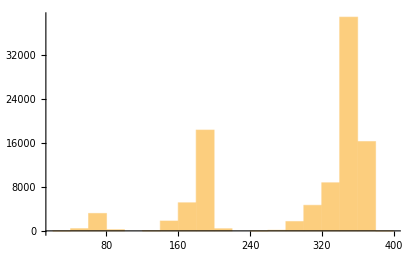

380

45

```mathematica
StringSplit/@TrainSet$ON$format3;
Length/@%//Histogram
Length/@%%//Max
Map[Function[sublist,Part[sublist,Position[sublist,"?"][[1,1]]+1;;]],%%%];
Length/@%//Max
```

### Save dataset

```mathematica
SetDirectory[NotebookDirectory[]]
Export["data_storage/dataset/example_ON/ON_data_valid.txt",TrainSet$ON$format3⟦1;;128⟧,"Text"]
Export["data_storage/dataset/example_ON/ON_data_test.txt",TrainSet$ON$format3⟦129;;3128⟧,"Text"]
Export["data_storage/dataset/example_ON/ON_data_train.txt",TrainSet$ON$format3⟦3129;;100000⟧,"Text"]
```

/Users/jaeha/repos/PolynomialSubstructure/MMA_package

data_storage/dataset/example_ON/ON_data_valid.txt

data_storage/dataset/example_ON/ON_data_test.txt

data_storage/dataset/example_ON/ON_data_train.txt

## Generating multi variable dataset

### Sample multi variable polynomials

```mathematica
(* original expression: degree 3 terms with maximum coefficient 5, maximum 3 terms *)
(* substitution: degree 3 terms with maximum coefficient 5, maximum 3 terms *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$multi$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1]},{a[0],a[1],a[2]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
(* examples *)
```

```mathematica
GenerateTrainSet$multi$CommonSet[3]//TableForm
```

-24 a[1]^9-108 a[0] a[1]^6 a[2]^2+64 a[1]^6 a[2]^3-162 a[0]^2 a[1]^3 a[2]^4-81 a[0]^3 a[2]^6 | -3 b[0]^3+b[1]^3 | 2 a[1]^3+3 a[0] a[2]^2 | 4 a[1]^2 a[2]
-192 a[0]^6 a[2]^3-20 a[0]^2 a[1]^4 a[2]^3+3 a[1]^6 a[2]^3-120 a[0]^3 a[1]^2 a[2]^4+27 a[0] a[1]^4 a[2]^4-180 a[0]^4 a[2]^5+81 a[0]^2 a[1]^2 a[2]^5+81 a[0]^3 a[2]^6 | 3 b[0]^3+5 b[0]^2 b[1]+3 b[1]^3 | a[1]^2 a[2]+3 a[0] a[2]^2 | -4 a[0]^2 a[2]
-90 a[0]^5 a[1]^3 a[2]-195 a[0]^4 a[1]^3 a[2]^2-420 a[0]^3 a[1]^3 a[2]^3-990 a[0]^2 a[1]^3 a[2]^4-1050 a[0] a[1]^3 a[2]^5-375 a[1]^3 a[2]^6 | 2 b[0]^2 b[1]+b[0] b[1]^2+3 b[1]^3 | 3 a[0]^2 a[1]+3 a[0] a[1] a[2] | -5 a[0] a[1] a[2]-5 a[1] a[2]^2

```mathematica
(* sample polynomials *)
```

```mathematica
TrainSet$multi$CommonSet = GenerateTrainSet$multi$CommonSet[110000];
```

```mathematica
TrainSet$multi$CommonSet = DeleteDuplicatesBy[TrainSet$multi$CommonSet,First];
Length[TrainSet$multi$CommonSet]
```

### Tokenize polynomials

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
GenerateTrainSet$multi$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,original,distributed},(*Read from existing table instead of generating*){expandedForm,short,sub1,sub2}=TrainSet$multi$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2];
{original}],{i,Min[n,Length[TrainSet$multi$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
GenerateTrainSet$multi$CommonSet$format3[3]//TableForm
```

+ * P 5 4 * ^ a0 P 5 * a1 ^ a2 P 3 + * N 1 5 3 * ^ a0 P 4 * ^ a1 P 2 ^ a2 P 3 + * P 5 1 * ^ a0 P 3 * ^ a1 P 3 ^ a2 P 3 + * N 5 4 * ^ a0 P 5 ^ a2 P 4 + * P 1 2 6 * ^ a0 P 4 * a1 ^ a2 P 4 + * P 1 0 2 * ^ a0 P 3 * ^ a1 P 2 ^ a2 P 4 + * P 2 7 * ^ a0 P 4 ^ a2 P 5 + * N 2 0 7 * ^ a0 P 3 * a1 ^ a2 P 5 * P 5 4 * ^ a0 P 3 ^ a2 P 6 ? + * P 2 * ^ b0 P 2 b1 + * N 1 * b0 ^ b1 P 2 * N 2 ^ b1 P 3 & + * N 3 * ^ a0 P 2 a2 * P 5 * a0 * a1 a2 & + * P 3 * a0 * a1 a2 * N 3 * a0 ^ a2 P 2
+ * N 2 7 * ^ a0 P 3 ^ a1 P 6 + * N 5 4 * ^ a0 P 2 ^ a1 P 7 + * N 3 6 * a0 ^ a1 P 8 + * N 1 1 6 ^ a1 P 9 + * P 2 1 6 * ^ a0 P 2 * ^ a1 P 6 a2 + * N 1 4 4 * ^ a0 P 4 * ^ a1 P 3 ^ a2 P 2 * P 3 2 * ^ a0 P 6 ^ a2 P 3 ? + * N 1 ^ b0 P 3 * P 4 ^ b1 P 3 & + * P 3 * a0 ^ a1 P 2 * P 2 ^ a1 P 3 & + * N 3 ^ a1 P 3 * P 2 * ^ a0 P 2 a2
+ * N 4 ^ a1 P 9 * P 3 * ^ a1 P 8 a2 ? + * N 4 ^ b0 P 3 * P 3 * ^ b0 P 2 b1 & ^ a1 P 3 & * ^ a1 P 2 a2

```mathematica
TrainSet$multi$format3=GenerateTrainSet$multi$CommonSet$format3[108000];
Length[TrainSet$multi$format3]
```

108000

```mathematica
(* dataset information *)
```

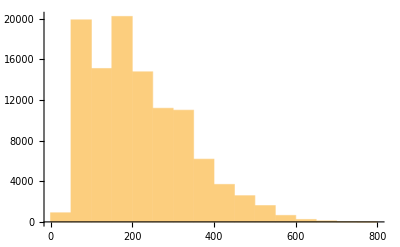

765

87

```mathematica
StringSplit/@TrainSet$multi$format3;
Length/@%//Histogram
Length/@%%//Max
Map[Function[sublist,Part[sublist,Position[sublist,"?"][[1,1]]+1;;]],%%%];
Length/@%//Max
```

### Save dataset

```mathematica
SetDirectory[NotebookDirectory[]]
Export["data_storage/dataset/example_multi/multi_data_valid.txt",TrainSet$multi$format3⟦1;;128⟧,"Text"]
Export["data_storage/dataset/example_multi/multi_data_test.txt",TrainSet$multi$format3⟦129;;3128⟧,"Text"]
Export["data_storage/dataset/example_multi/multi_data_train.txt",TrainSet$multi$format3⟦3129;;100000⟧,"Text"]
```

/Users/jaeha/repos/PolynomialSubstructure/MMA_package

data_storage/dataset/example_multi/multi_data_valid.txt

data_storage/dataset/example_multi/multi_data_test.txt

data_storage/dataset/example_multi/multi_data_train.txt

# Evaluation

#### Example evaluation

```mathematica
?EvaluateSimplificationResult
```

```mathematica
(* Above function load test dataset file and model prediction file on it. *)
(* Model prediction should be generated before this process *)
```

```mathematica
result=EvaluateSimplificationResult["../data_storage/dataset/example_ON/ON_data_test.txt","../data_storage/dataset/example_ON/example_ON_prediction.txt",False,True];
```

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

```mathematica
result
```

{0.,0.669,0.331}